```mathematica
Orientation={"(100)","(110)","(211)","(310)"}
head={"Nb-SnCl2","Nb-Sn(2)","Nb-Cl(3)","Substrate(4)"}
NbSnCl2={-6.25446479*10^4,-6.25595228*10^4,-7.74537475*10^4,-7.74392181*10^4}
NbSn={-6.16928633*10^4,-6.17102156*10^4,-7.66028881*10^4,-7.65884005*10^4}
NbCl={-6.00554572*10^4,-6.00741022*10^4,-7.49659281*10^4,-7.49508429*10^4}
NbSubstrate={-5.96299443*10^4,-5.96483043*10^4,-7.45398157*10^4,-7.45256638*10^4}
```

{(100),(110),(211),(310)}

{Nb-SnCl2,Nb-Sn(2),Nb-Cl(3),Substrate(4)}

{-62544.6,-62559.5,-77453.7,-77439.2}

{-61692.9,-61710.2,-76602.9,-76588.4}

{-60055.5,-60074.1,-74965.9,-74950.8}

{-59629.9,-59648.3,-74539.8,-74525.7}

```mathematica
Cl=-420.5060403851
SnCl2=-2.90704597*10^3
Sn=-2056.745039182
```

-420.506

-2907.05

-2056.75

```mathematica
Orientation
E ad Cl=NbCl-NbSubstrate-Cl
```

{(100),(110),(211),(310)}

{-5.00686,-5.29186,-5.60636,-4.67306}

```mathematica
Orientation
E ad SnCl2=NbSnCl2-NbSubstrate-SnCl2
```

{(100),(110),(211),(310)}

{-7.65763,-4.17253,-6.88583,-6.50833}

```mathematica
Orientation
E ad Sn=NbSn-NbSubstrate-Sn
```

{(100),(110),(211),(310)}

{-6.17396,-5.16626,-6.32736,-5.99166}

```mathematica
"d"
-1.68617641*10^5-(-1.65703947*10^5)-SnCl2
```

E_ad_SnCl2_(110)_5*5 SuperCell

-6.64803

```mathematica
SnCl2-Sn-2*Cl
```

-9.28885

```mathematica
length={2.388,2.688,2.988,3.288,3.588,3.888,4.188,4.488,4.788,5.088}
SnCl2 diff bond length={SnCl2,-2906.70264,-2906.07831,-2905.45305,-2904.91759,-2904.49268,-2904.16952,-2903.92612,-2903.74548,-2903.61388}
```

{2.388,2.688,2.988,3.288,3.588,3.888,4.188,4.488,4.788,5.088}

{-2907.05,-2906.7,-2906.08,-2905.45,-2904.92,-2904.49,-2904.17,-2903.93,-2903.75,-2903.61}

```mathematica
SnCl2 diff bond length-SnCl2
```

{0.,0.34333,0.96766,1.59292,2.12838,2.55329,2.87645,3.11985,3.30049,3.43209}

```mathematica
Ebond=Table[{length[[i]],SnCl2 diff bond length[[i]]-SnCl2},{i,1,9}]
```

{{2.388,0.},{2.688,0.34333},{2.988,0.96766},{3.288,1.59292},{3.588,2.12838},{3.888,2.55329},{4.188,2.87645},{4.488,3.11985},{4.788,3.30049}}

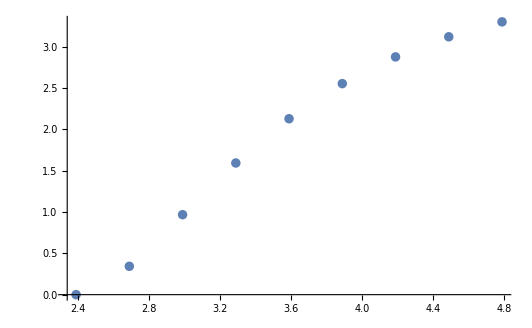

```mathematica
ListPlot[Ebond]
```

```mathematica
f=Interpolation[Ebond]
```

InterpolatingFunction[…]

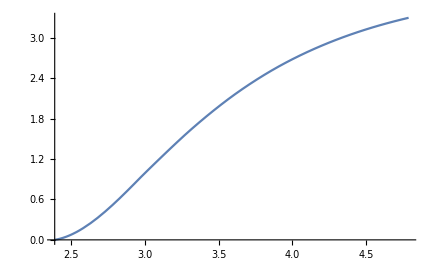

```mathematica
Plot[f[x],{x,2.388,4.788}]
```

```mathematica
(f[3.5]-f[3.7])+(f[4.1]-f[4.4])
```

-0.582443

```mathematica
headlayer1={"(110)","(100)","(310)","(211)"}
```

{(110),(100),(310),(211)}

```mathematica
layer1={-1.53180392*10^4,-8.68843551*10^3,-8.68619978*10^3,-8.68767206*10^3}
layer2={-1.73785951*10^4,-1.07494428*10^4,-1.07470680*10^4,-1.07485738*10^4}
```

{-15318.,-8688.44,-8686.2,-8687.67}

{-17378.6,-10749.4,-10747.1,-10748.6}

```mathematica
headlayer1
layer2-layer1-Sn
```

{(110),(100),(310),(211)}

{-3.81086,-4.26225,-4.12318,-4.1567}

```mathematica
(-16485.69789-8*Sn)/8
```

-3.9672